```mathematica
(*Problem 1*)
```

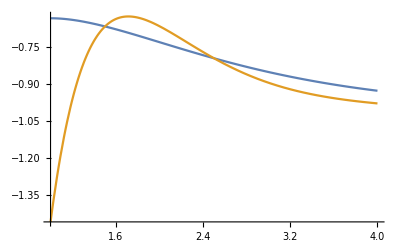

```mathematica
f[x_]= x*Exp[-x] - 1;
g[x_] = f[x] + D[f[x],x]*(x-2.5)+ .5*D[f[x],x,x]*(x-2.5)^2 + (1/3!)*D[f[x],x,x,x]*(x-2.5)^3;
Plot[{f[x],g[x]},{x,1,4}]
```

```mathematica
h[x_] = (f[x]-g[x])^2;
NormError1 = Sqrt[Integrate[h[x],{x,1,4}]]
```

0.279483

```mathematica
MeanNormError1 = (1/(4-1))*Sqrt[Integrate[h[x],{x,1,4}]]
```

0.0931611

```mathematica
(*Problem 2*)
(*Part a*)
```

```mathematica
f[x_]= x*Exp[-x] - 1;
Px= {};
Px1 = {};
y = {};
For[i = 1, i ≤ 4, ++i,
newrow1= {};
newrow2 = {};
For[j=1, j ≤ 4, ++j,
AppendTo[newrow1,i^(j-1)];
AppendTo[newrow2, x^(j-1)];
];
AppendTo[Px, newrow1];
AppendTo[Px1,newrow2];
AppendTo[y, f[i]];
];
Print[MatrixForm[Px]]
Print[MatrixForm[Px1]]
Print[MatrixForm[y]]
```

(1 | 1 | 1 | 1
1 | 2 | 4 | 8
1 | 3 | 9 | 27
1 | 4 | 16 | 64)

(1 | x | x^2 | x^3
1 | x | x^2 | x^3
1 | x | x^2 | x^3
1 | x | x^2 | x^3)

(-1+1/ⅇ
-1+2/ⅇ^2
-1+3/ⅇ^3
-1+4/ⅇ^4)

```mathematica
LinearSolve[Px,y]
```

{(-4+12 ⅇ-12 ⅇ^2+4 ⅇ^3-ⅇ^4)/ⅇ^4,(22-63 ⅇ+57 ⅇ^2-13 ⅇ^3)/(3 ⅇ^4),(-8+21 ⅇ-16 ⅇ^2+3 ⅇ^3)/(2 ⅇ^4),(4-9 ⅇ+6 ⅇ^2-ⅇ^3)/(6 ⅇ^4)}

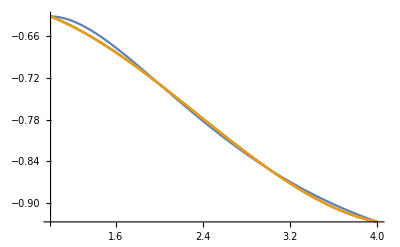

```mathematica
(*Part b*)
Poly[x_] = Px1.LinearSolve[Px,y];
Plot[{f[x],Poly[x]},{x,1,4}]
```

```mathematica
(*Part c*)
h2[x_] = Norm[f[x]-Poly[x]^2];
NormError2 = Sqrt[Integrate[h2[x],{x,1,4}]]
```

1/(ⅇ^4 √(70/(512+594 ⅇ+1314 ⅇ^2-205 ⅇ^3+874 ⅇ^4-846 ⅇ^5-598 ⅇ^6-385 ⅇ^7+840 ⅇ^8)))

```mathematica
MeanNormError2 = (1/(4-1))*Sqrt[Integrate[h2[x],{x,1,4}]]
```

1/(3 ⅇ^4 √(70/(512+594 ⅇ+1314 ⅇ^2-205 ⅇ^3+874 ⅇ^4-846 ⅇ^5-598 ⅇ^6-385 ⅇ^7+840 ⅇ^8)))

```mathematica
(*The polynomial interpolation is better than the cubic Taylor interpolation.*)
```

```mathematica
(*Problem 3*) 
q[x_] = 1/(1+x^2);
Px2= {};
Px3 = {};
y2 = {};
For[i = -2, i ≤ 2, ++i,
newrow3 ={};
newrow4 = {};
For[j=2, j ≤ 5, ++j,
AppendTo[newrow3,i^(j-1)];
AppendTo[newrow4, x^(j-2)];
];
AppendTo[Px2, newrow3];
AppendTo[Px3,newrow4];
AppendTo[y2, q[i]]
];
Print[MatrixForm[Px2]]
Print[MatrixForm[Px3]]
Print[MatrixForm[y2]]
```

(-2 | 4 | -8 | 16
-1 | 1 | -1 | 1
0 | 0 | 0 | 0
1 | 1 | 1 | 1
2 | 4 | 8 | 16)

(1 | x | x^2 | x^3
1 | x | x^2 | x^3
1 | x | x^2 | x^3
1 | x | x^2 | x^3
1 | x | x^2 | x^3)

(1/5
1/2
1
1/2
1/5)

```mathematica
(*Since one of the x's is 0, one of the rows is entirely zero, this means we would need to use Langrage's interpolation, but alas, it's too late, homework is due now :( *).
```

```mathematica
LinearSolve[Px2,y2]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

```mathematica
LinearSolve[{{-2,4,-8,16},{-1,1,-1,1},{0,0,0,0},{1,1,1,1},{2,4,8,16}},{1/5,1/2,1,1/2,1/5}]
Poly2[x_] = Px3.LinearSolve[Px2,y]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{-2,4,-8,16},{-1,1,-1,1},{0,0,0,0},{1,1,1,1},{2,4,8,16}},{1/5,1/2,1,1/2,1/5}]

LinearSolve::lslc: Coefficient matrix and target vector(s) or matrix do not have the same dimensions.

{{1,x,x^2,x^3},{1,x,x^2,x^3},{1,x,x^2,x^3},{1,x,x^2,x^3},{1,x,x^2,x^3}}.LinearSolve[{{-2,4,-8,16},{-1,1,-1,1},{0,0,0,0},{1,1,1,1},{2,4,8,16}},{1/2,1/5,1/10,1/17}]

```mathematica
h3[x_] = (f[x]-Poly2[x])^2;
NormError3 = Sqrt[Integrate[h3[x],{x,1,4}]]
```

```mathematica
MeanNormError3 = (1/(4-1))*Sqrt[Integrate[h3[x],{x,1,4}]]
```